```mathematica
(*2.3a*)
(*What is ω for the two systems (1)and(2),respectively?*)
(*System (1)*)
x1[x,y]=μ*x-6*y-2*x^3;
y1[x,y]=6*x+μ*y+4*y^3;
(*System (2)*)
x2[x,y]=μ*x+y-x^2;
y2[x,y]=-x+μ*y+2*x^2;
(*Hopf bif. at origin for μ=0 with ẏ = ωx, ẋ = -ωy:*)Eqs={{x1[x,y],y1[x,y]},{x2[x,y],y2[x,y]}}/. μ->0;
Eqs[[1]]
```

```mathematica
{-2 x^3-6 y,6 x+4 y^3}
(*For system one we can see that-6y=-ωy and 6x=ωx -> ω1=6;*)
```

```mathematica
Eqs[[2]]
```

```mathematica
{-x^2+y,-x+2 x^2}
(*For system two we get y=-ωy and-x=ωx,thus ω2=-1;*)
```

```mathematica
(*2.3b) Determine f and g for the systems (1) and (2)*)
(* x=-ωy+f(x,y), y=ωx+g(x,y);and the computed equations(Eqs) we get f(x,y) and g(x,y) by comparison;From system one -> f1(x,y)=-2 x^3 and g1(x,y)=4 y^3;
From system two -> f2(x,y)=-x^2 and g2(x,y)=2 x^2;*)
```

```mathematica
(*2.3c) Determine a for the two systems (1)and (2)*)
(*System one*)
Clear["Global`*"]
ω={6,-1};
fx=D[{-2x^3,-x^2},x];
fxx=D[fx,x];
fxxx=D[fxx,x];
fxy=D[fx,y];
fxyy=D[fxy,y];
fy=D[{-2x^3,-x^2},y];
fyy=D[fy,y];
gx=D[{4y^3,2x^2},x];
gxx=D[gx,x];
gxxy=D[gxx,x];
gxy=D[gx,y];
gy=D[{4y^3,2x^2},y];
gyy=D[gy,y];
gyyy=D[gyy,y];
Solve[16 a==fxxx⟦1⟧+fxyy⟦1⟧+gxxy⟦1⟧+gyyy⟦1⟧+1/ω⟦1⟧*(fxy⟦1⟧*(fxx⟦1⟧+fyy⟦1⟧)-gxy⟦1⟧*(gxx⟦1⟧+gyy⟦1⟧)-fxx⟦1⟧*gxx⟦1⟧+fyy⟦1⟧*gyy⟦1⟧),a]
Solve[16a==fxxx⟦2⟧+fxyy⟦2⟧+gxxy⟦2⟧+gyyy⟦2⟧+1/ω⟦2⟧*(fxy⟦2⟧*(fxx⟦2⟧+fyy⟦2⟧)-gxy⟦2⟧*(gxx⟦2⟧+gyy⟦2⟧)-fxx⟦2⟧*gxx⟦2⟧+fyy⟦2⟧*gyy⟦2⟧),a]
```

{{a→3/4}}

{{a→-1/2}}

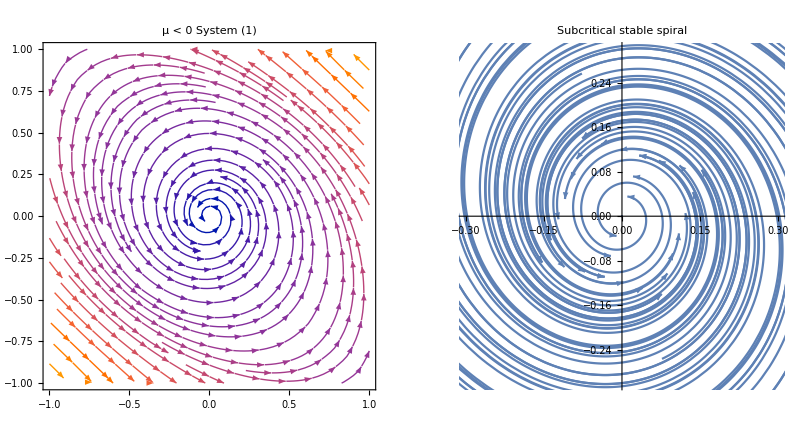

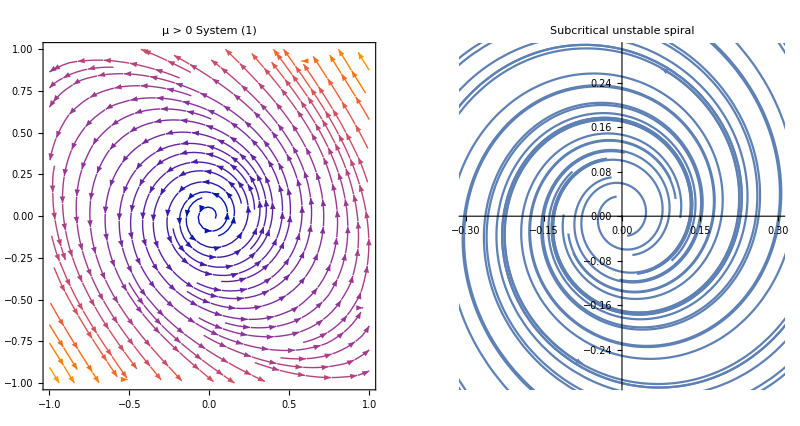

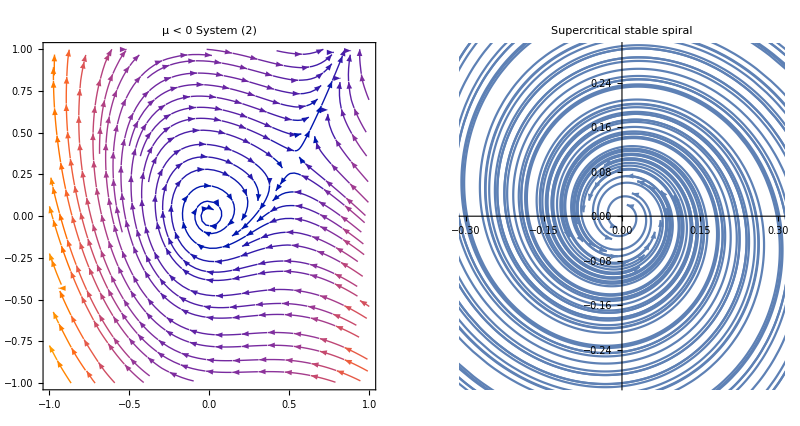

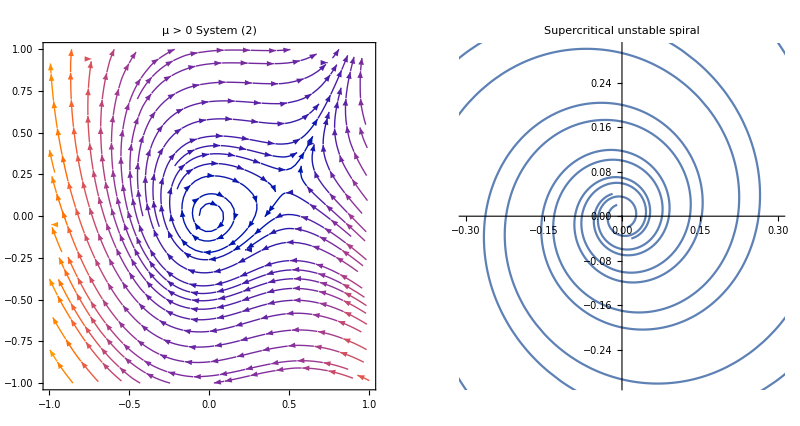

```mathematica
(*2.3d*)
(*Draw phase portraits of the global dynamics for positive and negative μ for each of the systems (1) and (2). Make sure that these phase portraits verify the criteria you found in subtask*)

(*From 2.3c we see that system (1) is subcritical a<0; and system (2) is supercritical a<0*)
(*subcritical a<0*)
(*First case where μ < 0 *)
xDot[x_,y_,μ_] := μ x - 6y -2x^3;
yDot[x_,y_,μ_] := 6x + μ y + 4y^3;
mu1={-1,1};
Eqs1=Transpose[{x1[x,y],y1[x,y]}/. μ->mu1];
p1=StreamPlot[Eqs1[[1]],{x,-1,1},{y,-1,1},PlotLabel->"μ < 0\nSystem (1)"];
minx=-0.3;  maxx=0.3; miny=-0.3; maxy=0.3;
s[x0_, y0_]=NDSolve[{x'[t]==xDot[x[t],y[t],μ],y'[t]==yDot[x[t],y[t],μ], x[0]==x0,y[0]==y0}/. μ->-1,{x,y},{t,-1,1}];
initialCondition=Join[Table[{0,y},{y,miny,maxy,0.1}],Table[{minx,y},{y,miny,maxy,0.1}],Table[{maxx,y},{y,miny,maxy,0.1}],Table[{x,miny},{x,minx,maxx,0.1}],Table[{x,maxy},{x,minx,maxx,0.1}]];
p12 =Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/. s[initialCondition[[i,1]],initialCondition[[i,2]]]],{t,-1,1},PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[initialCondition]}]/. Line[x_]:>{Arrowheads[{0.,0.05, 0.05, 0.05, 0.}],Arrow[x]}, PlotLabel-> "Subcritical stable spiral"];

(*Second case where μ > 0 *)
p2=StreamPlot[Eqs1[[2]],{x,-1,1},{y,-1,1},PlotLabel->"μ > 0\nSystem (1)"];
s[x0_, y0_]=NDSolve[{x'[t]==xDot[x[t],y[t],μ],y'[t]==yDot[x[t],y[t],μ], x[0]==x0,y[0]==y0}/. μ->1,{x,y},{t,-1,1}];
initialCondition=Join[Table[{0,y},{y,miny,maxy,0.1}],Table[{minx,y},{y,miny,maxy,0.1}],Table[{maxx,y},{y,miny,maxy,0.1}],Table[{x,miny},{x,minx,maxx,0.1}],Table[{x,maxy},{x,minx,maxx,0.1}]];
p22 = Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/. s[initialCondition[[i,1]],initialCondition[[i,2]]]],{t,-1,1},PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[initialCondition]}]/. Line[x_]:>{Arrowheads[{0.,0.05, 0.05, 0.05, 0.}],Arrow[x]}, PlotLabel-> "Subcritical unstable spiral"];

(*System (2): supercritical case*)
(*First case where μ < 0 *)
xDot2[x_,y_,μ_] := μ x +y -x^2;
yDot2[x_,y_,μ_] := -x + μ y + 2x^2;

mu2={-0.1,0.1};
Eqs2=Transpose[{x2[x,y],y2[x,y]}/. μ->mu2];p3=StreamPlot[Eqs2[[1]],{x,-1,1},{y,-1,1},PlotLabel->"μ < 0\nSystem (2)"];
s[x0_, y0_]=NDSolve[{x'[t]==xDot[x[t],y[t],μ],
y'[t]==yDot[x[t],y[t],μ], x[0]==x0,y[0]==y0}/. μ->-1,{x,y},{t,-1.5,1.5}];
initialCondition=Join[Table[{0,y},{y,miny,maxy,0.1}],Table[{minx,y},{y,miny,maxy,0.1}],Table[{maxx,y},{y,miny,maxy,0.1}],Table[{x,miny},{x,minx,maxx,0.1}],Table[{x,maxy},{x,minx,maxx,0.1}]];
p32=Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/. s[initialCondition[[i,1]],initialCondition[[i,2]]]],{t,-1.5,1.5},PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[initialCondition]}]/. Line[x_]:>{Arrowheads[{0.,0.05, 0.05, 0.05, 0.}],Arrow[x]}, PlotLabel-> "Supercritical stable spiral"];
(*Second case where μ > 0 *)
p4=StreamPlot[Eqs2[[2]],{x,-1,1},{y,-1,1},PlotLabel->"μ > 0\nSystem (2)"];
s[x0_, y0_]=NDSolve[{x'[t]==xDot[x[t],y[t],μ],
y'[t]==yDot[x[t],y[t],μ], x[0]==x0,y[0]==y0}/. μ->1,{x,y},{t,-1.5,1.5}];
initialCondition=Join[Table[{0,y},{y,miny,maxy,0.1}],Table[{minx,y},{y,miny,maxy,0.1}],Table[{maxx,y},{y,miny,maxy,0.1}],Table[{x,miny},{x,minx,maxx,0.1}],Table[{x,maxy},{x,minx,maxx,0.1}]];
p42=Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/. s[initialCondition[[i,1]],initialCondition[[i,2]]]],{t,-1.5,1.5},PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[initialCondition]}]/. Line[x_]:>{Arrowheads[{0.,0.05, 0.05, 0.05, 0.}],Arrow[x]}, PlotLabel-> "Supercritical unstable spiral"];
GraphicsRow[{p1,p12}]
GraphicsRow[{p2,p22}]
GraphicsRow[{p3,p32}]
GraphicsRow[{p4,p42}]
(*From the plots we can draw the conclustion that they agree with what we predicted thus verifying our criteria in 2.3c see page 254-255 in the book,fig 8.2.3 and 8.2.5.*)
```